## Homework 1.5 Simulate a DNA-strand-displacement reaction

```mathematica
solve[r1i_,r2i_,k_,end_]:=NDSolve[{
r1'[t]==-k*r1[t]*r2[t],
r2'[t]==-k*r1[t]*r2[t],
p1'[t]==k*r1[t]*r2[t],
p2'[t]==k*r1[t]*r2[t],
p1[0]==0,
p2[0]==0,
r1[0]==r1i,
r2[0]==r2i
},{r1,r2,p1,p2},{t,0,end}]
```

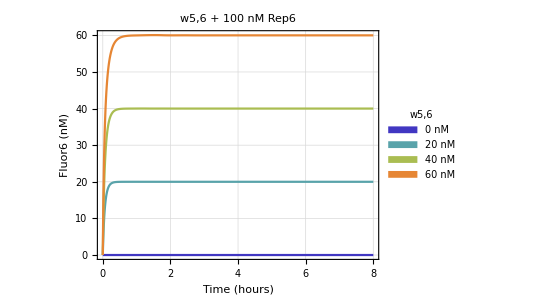

```mathematica
r1i=100*10^-9;
r2i={0*10^-9,20*10^-9,40*10^-9,60*10^-9};
kHours=5*10^4*60*60;
time=8;
s=Table[solve[r1i,r2i[[i]],kHours,time],{i,1,Length[r2i]}];
eval=Table[Evaluate[p1[t]/.s[[i]]]/10^-9,{i,1,Length[s]}];
Plot[eval,{t,0,time},PlotLabel->Style["w5,6 + 100 nM Rep6",20],Frame->True,FrameLabel->{"Time (hours)","Fluor6 (nM)"},PlotStyle->Table[{Thick,ColorData["Rainbow"][i]},{i,0.12,0.96,0.96/4}],PlotLegends->Placed[SwatchLegend[Automatic,{"0 nM","20 nM","40 nM","60 nM"},LegendLabel->"w5,6",LegendMarkerSize->14],Right],LabelStyle->Directive[Gray,FontSize->20,FontFamily->"Helvetica"],
GridLines->Automatic,PlotRange->All,AspectRatio->1/1.3,ImageSize->400]
```